```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching "Global`*".

```mathematica
$Assumptions={n}∈Integers ∧n>0
```

# Mathematica for Engineering Systems I

## Introduction

The Applied Physics curriculum is being modified, starting from study year 2018, with respect to tools we want students to be professionalized at. We will drop Matlab in favour of Python as a programming and data analysis tool. This change has 
At his point I do not want to go into the details of the motivation, and the choices that have to be made, but only address the possibilities of Mathematica to help you with the job of modelling and simulation.

In this document, an overview is given of the functions that replace the various functions, modules and applications in Matlab. For the replacement of Simulink, we already elaborated on the drop of the graphical programming of this modelling language: after module 5 nobody, no research group and no external company (we know off) uses Simulink. However the need for the simulation of calculation of a non-linear dynamic system remains.

## Intended Content

Differential equations and Laplace Transforms:

Transfer-functions and State-Space models:

Fourier Transforms and Fourier Series (continuous):

Discrete-time signals: difference equations:

Discrete Fourier Transform:

FIR-filter design:

z-Transform

IIR-filter design

Stochastic Signals description:

## Continuous-time systems

Differential Equations

Below you will find an method of solving differential equations via state-space systems and transfer functions, generating Bode-Plots, Nyquist Plots, and responses.

#### First-order system

Differential equations can be described in Mathematica and also solved. Let start with a simple first order differential equation:

```mathematica
eqn1=y'[t]+ 1/τ y[t] ==  UnitStep[t]
```

y[t]/τ+y'[t]==UnitStep[t]

The differential equation can also be solved, e.g. with initial condition y[0]=0

```mathematica
dsol1=DSolve[{eqn1,y[0]==0},y[t],t]
```

{{y[t]→ⅇ^(-t/τ) (-1+ⅇ^(t/τ)) τ UnitStep[t]}}

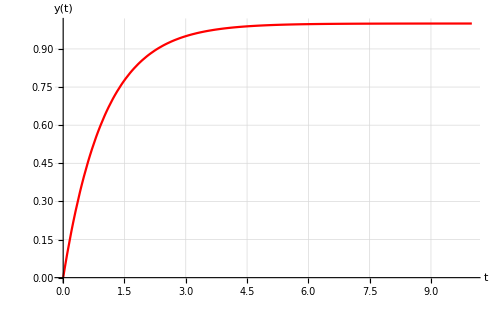

```mathematica
Plot[y[t]/.dsol1/.τ->1,{t,0,10},PlotRange->Full,GridLines->Automatic,GridLinesStyle->Dotted,ImageSize->500,AxesLabel->{"t","y(t)"},PlotStyle->Red,BaseStyle->12]
```

#### Second-order system

Let us now define a second-order system and solve that one with initial conditions and no input.

```mathematica
eqn2=y''[t]+ 2 ζ ω0 y'[t]+ω0^2 y[t]==0
```

ω0^2 y[t]+2 ζ ω0 y'[t]+y''[t]==0

```mathematica
initc={y'[0]== 0,y[0]==2}
```

{y'[0]==0,y[0]==2}

```mathematica
dsol2=DSolve[Flatten[{eqn2,initc}],y[t],t]
```

{{y[t]→1/((-1+ζ^2) ω0)(-ⅇ^(t (-ζ ω0-√((-1+ζ^2) ω0^2))) ω0-ⅇ^(t (-ζ ω0+√((-1+ζ^2) ω0^2))) ω0+ⅇ^(t (-ζ ω0-√((-1+ζ^2) ω0^2))) ζ^2 ω0+ⅇ^(t (-ζ ω0+√((-1+ζ^2) ω0^2))) ζ^2 ω0-ⅇ^(t (-ζ ω0-√((-1+ζ^2) ω0^2))) ζ √((-1+ζ^2) ω0^2)+ⅇ^(t (-ζ ω0+√((-1+ζ^2) ω0^2))) ζ √((-1+ζ^2) ω0^2))}}

```mathematica
y[t]/.dsol2/.{ζ->1/2,ω0->2}
```

{-2/3 (-3/2 ⅇ^((-1-ⅈ √3) t)-1/2 ⅈ √3 ⅇ^((-1-ⅈ √3) t)-3/2 ⅇ^((-1+ⅈ √3) t)+1/2 ⅈ √3 ⅇ^((-1+ⅈ √3) t))}

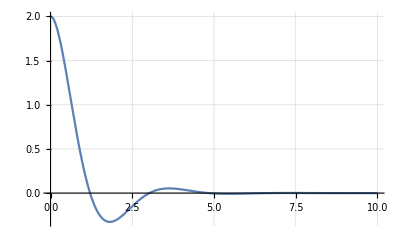

```mathematica
Plot[y[t]/.dsol2/.{ζ->0.5,ω0->2},{t,0,10},PlotRange->Full,GridLines->Automatic]
```

#### Solving differential equations is not the core of this course.

Although it is possible to solve differential equations with Mathematica, it is not the core bossiness in this course. The main subject is to get acquainted with various tools and develop a broader insight in the system of modelling. In the previous examples the differential equations were already formulated with the useful parameters: time constant τ for the first order system, and natural frequency ω0 and damping coefficient ζ for the second order system. These parameters can be derived from the plots of the output.

An other way of solving the differential equations is the application of the Laplace transform.

Laplace Transform

### Direct Laplace Transforms and Inverse Laplace Transforms

First we start with a few stand-alone Laplace transforms and inverse transforms. Basically you can check the Laplace pairs in the standard table.

#### a.

```mathematica
LaplaceTransform[Cos[ω t],t,s]
```

s/(s^2+ω^2)

#### b.

```mathematica
InverseLaplaceTransform[ω/(s^2+ω^2),s,t]
```

Sin[t ω]

#### c.

```mathematica
LaplaceTransform[ⅇ^(-γ t)Cos[ω t],t,s]
```

(s+γ)/((s+γ)^2+ω^2)

```mathematica
InverseLaplaceTransform[ⅇ^(-s Subscript[t, 0]),s,t]
```

InverseLaplaceTransform[ⅇ^(-s t_0),s,t]

### Laplace Transform to solve Differential equations

Now we apply Laplace to solve differential equations.

#### a.

```mathematica
lteqn1=LaplaceTransform[y'[t]-3 y[t]==0,t,s]
```

-3 LaplaceTransform[y[t],t,s]+s LaplaceTransform[y[t],t,s]-y[0]==0

```mathematica
Solve[lteqn1/.y[0]-> 1,LaplaceTransform[y[t],t,s]]
```

{{LaplaceTransform[y[t],t,s]→1/(-3+s)}}

```mathematica
InverseLaplaceTransform[%,s,t]
```

{{y[t]→ⅇ^(3 t)}}

#### b.

```mathematica
lteqn2=LaplaceTransform[y''[t]+3 y'[t]+2 y[t]==0,t,s]
```

2 LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]+3 (s LaplaceTransform[y[t],t,s]-y[0])-s y[0]-y'[0]==0

```mathematica
Solve[lteqn2/.{y'[0]->0,y[0]->2},LaplaceTransform[y[t],t,s]]
```

{{LaplaceTransform[y[t],t,s]→(2 (3+s))/(2+3 s+s^2)}}

```mathematica
InverseLaplaceTransform[%,s,t]
```

{{y[t]→2 ⅇ^(-2 t) (-1+2 ⅇ^t)}}

### Inverse Laplace Transform of a Transfer Function

#### a.

```mathematica
InverseLaplaceTransform[10/(s^3+4 s^2+9 s + 10),s,t]
```

10 (ⅇ^(-2 t)/5-1/20 ⅇ^((-1-2 ⅈ) t) ((2-ⅈ)+(2+ⅈ) ⅇ^(4 ⅈ t)))

```mathematica
%//FullSimplify
```

ⅇ^(-2 t) (2+ⅇ^t (-2 Cos[2 t]+Sin[2 t]))

#### b.

ii

```mathematica
yb2[t_]=InverseLaplaceTransform[1/(s+1)^4,s,t]
```

1/6 ⅇ^-t t^3

iii

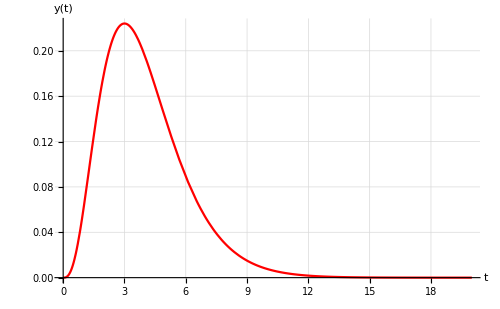

```mathematica
Plot[yb2[t],{t,0,20},GridLines->Automatic,GridLinesStyle->Dotted,ImageSize->500,AxesLabel->{"t","y(t)"},PlotStyle->Red,BaseStyle->12]
```

```mathematica
yb3[t_]=InverseLaplaceTransform[(s-3)/((s+3)^2+6),s,t]
```

(ⅇ^(-3 t) (√6 Cos[√6 t]-6 Sin[√6 t]))/(√6)

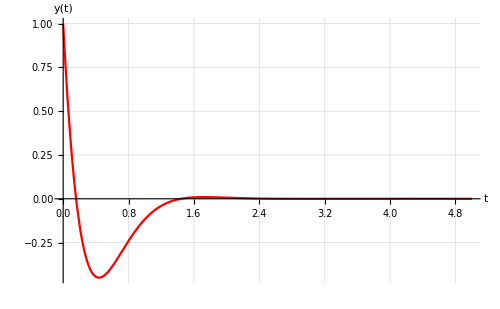

```mathematica
Plot[yb3[t],{t,0,5},PlotRange->All,GridLines->Automatic,GridLinesStyle->Dotted,ImageSize->500,AxesLabel->{"t","y(t)"},PlotStyle->Red,BaseStyle->12]
```

### Inverse Laplace Transform of a step function and a delay

```mathematica
InverseLaplaceTransform[ⅇ^-s/s,s,t]
```

HeavisideTheta[-1+t]

### Partial fraction decomposition

Techniques used with the Laplace transforms can also be used separately.

```mathematica
expr=(s^4+8 s^3+16 s^2+9 s+6)/(s^3+6 s^2+11 s+6)
```

(6+9 s+16 s^2+8 s^3+s^4)/(6+11 s+6 s^2+s^3)

```mathematica
InverseLaplaceTransform[expr,s,t]
```

-6 ⅇ^(-3 t)-4 ⅇ^(-2 t)+3 ⅇ^-t+2 DiracDelta[t]+DiracDelta'[t]

Perform a partial fraction decomposition of the transfer function

```mathematica
exprpf=Apart[expr]
```

2+s+3/(1+s)-4/(2+s)-6/(3+s)

and calculate the inverse Laplace Transform

```mathematica
InverseLaplaceTransform[exprpf,s,t]
```

-6 ⅇ^(-3 t)-4 ⅇ^(-2 t)+3 ⅇ^-t+2 DiracDelta[t]+DiracDelta'[t]

The results are the same, as it should be. Now a direct relation between the terms can be made.

### From Laplace to differential equation

```mathematica
tfToDiff[tf_,s_,t_,y_,u_]:=Module[{rhs,lhs,n,m},rhs=Numerator[tf];
lhs=Denominator[tf];
rhs=rhs/.m_. s^n_.->m D[u[t],{t,n}];
lhs=lhs/.m_. s^n_.->m D[y[t],{t,n}];
lhs==rhs]
tf=(5s)/(s^2+4s+25);
tf=C0 s/(R0 C0 s+1);
eq=tfToDiff[tf,s,t,y,u]
```

1+C0 R0 y'[t]==C0 u'[t]

Transfer functions

With the use of Laplace, a transfer function can be constructed and with this transfer function a transfer function model.

#### First example

```mathematica
sys0=TransferFunctionModel[25/(s^2+4 s+25),s]
```

25/(25+4 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s1125251FalseFalseFalseAutomaticNoneAutomatic

And extract the characteristics, like zero’s and poles.

```mathematica
TransferFunctionZeros[sys0]
```

{{{}}}

```mathematica
TransferFunctionPoles[sys0]//N
```

{{{-2.-4.58258 ⅈ,-2.+4.58258 ⅈ}}}

#### Define a general transfer function of second-order:

```mathematica
sys1=TransferFunctionModel[1/(s^2+2 ζ ω0 s + ω0^2),s]
```

1/(ω0^2+2 ζ ω0 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s111$CellContext`s1FalseFalseFalseAutomaticNoneAutomatic

Define a set of parameters for exploration of the second-order system:

```mathematica
param={{ζ->0.2,ω0->2},{ζ->1/2 √2,ω0->2},{ζ->2,ω0->2}}
```

{{ζ→0.2,ω0→2},{ζ→1/(√2),ω0→2},{ζ→2,ω0→2}}

```mathematica
rsys1=OutputResponse[sys1/.param[[1]],UnitStep[t],t];
```

```mathematica
rsys2=OutputResponse[sys1/.param[[1]],DiracDelta[t-3],t];
```

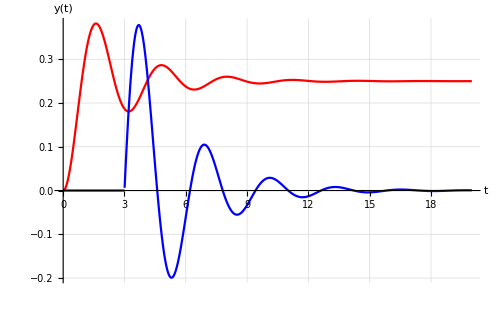

```mathematica
Plot[{rsys1,rsys2},{t,0,20},PlotRange->Full,GridLines->Automatic,GridLinesStyle->Dotted,ImageSize->500,AxesLabel->{"t","y(t)"},PlotStyle->{Red,Blue},BaseStyle->12]
```

This method can be extended to multiple-input, multiple-output systems. You can also directly define transfer functions:

#### Calculate the poles of the transfer function

First in the general case

```mathematica
poles=Solve[ω0^2+2 ζ ω0 s+s^2==0,s]
```

{{s→-ζ ω0-√(-ω0^2+ζ^2 ω0^2)},{s→-ζ ω0+√(-ω0^2+ζ^2 ω0^2)}}

Now for the given sets of parameter values:

```mathematica
poles/.param//N//MatrixForm
```

((s→-0.4-1.95959 ⅈ) | (s→-0.4+1.95959 ⅈ)
(s→-1.41421-1.41421 ⅈ) | (s→-1.41421+1.41421 ⅈ)
(s→-7.4641) | (s→-0.535898))

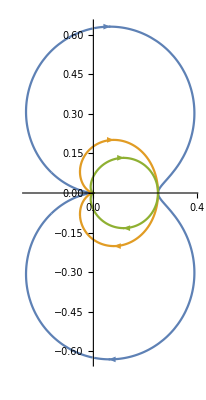

```mathematica
NyquistPlot[sys1/.param]
```

State-Space Formalism

Beside transfer function models, also state-space models can be constructed.

### Second order system

We start here after writing down the first-order differential equations of our model. Writing this in matrix notation, should give us four equations that represent the system: the so-called A, B, C and D matrices.

```mathematica
aa4={{-b/m,-1/m},{k,0}};
```

```mathematica
MatrixForm[aa4]
```

(-b/m | -1/m
k | 0)

```mathematica
bb4={{1/m},{0}};
```

```mathematica
MatrixForm[bb4]
```

(1/m
0)

```mathematica
cc4={{1,0}};
```

```mathematica
MatrixForm[cc4]
```

(1 | 0)

```mathematica
dd4={{0}};
```

```mathematica
MatrixForm[dd4]
```

(0)

Let us set some values for the parameters in the system for calculation.

```mathematica
cond4={m->4,b->2,k->4}
```

{m→4,b→2,k→4}

The State=Space model can be constructed directly from the matrices:

```mathematica
ss4=StateSpaceModel[{aa4,bb4,cc4,dd4}]
```

-b/m-1/m1/mk00100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

You recognize the matrices you defined above.

```mathematica
CharacteristicPolynomial[aa4,s]
```

k/m+(b s)/m+s^2

From this State-Space system, a Transfer function model can be constructed. In this case it is not that complicated, since we only have one input, and one output. For a multiple input and multiple output system this wil generate a matrix of transfer functions, relating every input to every output.

In general case this gives:

```mathematica
tf4g=TransferFunctionModel[ss4,s]
```

s/(m (k/m+(b s)/m+s^2))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11$CellContext`m$CellContext`k1FalseFalseFalseAutomaticNoneAutomatic

The denominator of the Transfer Function can be recognized as the characteristic polynomial of the A-matrix.

Using the parameter values we defined above we obtain a form for further processing, like Bode Plots and input responses.

```mathematica
tf4=TransferFunctionModel[ss4/.cond4,s]
```

s/(4 (1+s/2+s^2))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11111FalseFalseFalseAutomaticNoneAutomatic

```mathematica
rsys4ga=OutputResponse[tf4,UnitStep[t],t];
```

```mathematica
rsys4gb=OutputResponse[tf4,DiracDelta[t],t];
```

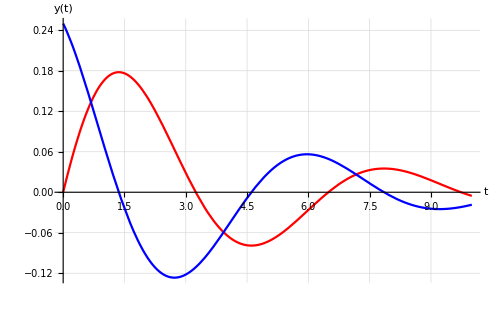

```mathematica
Plot[{rsys4ga,rsys4gb},{t,0,10},GridLines->Automatic,GridLinesStyle->Dotted,ImageSize->500,AxesLabel->{"t","y(t)"},PlotStyle->{Red,Blue},BaseStyle->12]
```

### State-Space with initial conditions

```mathematica
aa5={{-0.5572,-0.7814},{0.7814,0}};
```

```mathematica
bb5={{1},{0}};
```

```mathematica
cc5={{1.9691,6.4493}};
```

```mathematica
dd5={{0}};
```

```mathematica
sys5=StateSpaceModel[{aa5,bb5,cc5,dd5}]
```

-0.5572-0.781410.7814001.96916.44930StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

```mathematica
x5i={1,0}
```

{1,0}

```mathematica
{x5a,x5b}=StateResponse[{sys5,x5i},0,{t,0,20}]
```

{InterpolatingFunction[{{0., 20.}}, <>][t],InterpolatingFunction[{{0., 20.}}, <>][t]}

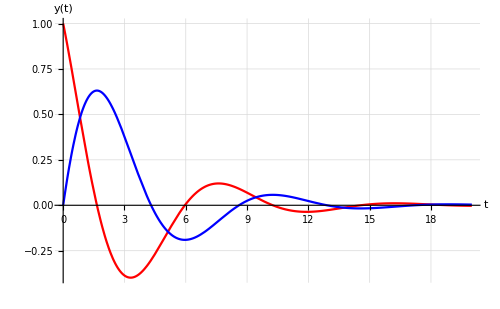

```mathematica
Plot[{x5a,x5b},{t,0,20},PlotRange->All,GridLines->Automatic,ImageSize->500,AxesLabel->{"t","y(t)"},PlotStyle->{Red,Blue},BaseStyle->12]
```

## From Differential equations

```mathematica
Clear[y,u,t];
eq=3 y''[t]+2 y'[t]+y[t]==u[t];
ss=StateSpaceModel[{eq},{{y'[t],0},{y[t],0}},{{u[t],0}},{y[t]},t];
ss=MinimalStateSpaceModel[ss]
```

-2/3-1/31/3100010StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNone,Automatic,{{u[t],0}},Automatic,t

```mathematica
tf=Simplify[TransferFunctionModel[ss]]
```

1/(1+2 s+3 s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s11111FalseFalseFalseAutomaticNone,{u[s]}

#### Transferfunction ↔ State-Space Model

```mathematica
tf6=TransferFunctionModel[(1+s)/(s^2+4 s + 6),s]
```

(1+s)/(6+4 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11161FalseFalseFalseAutomaticNoneAutomatic

and construct the State-Space model from this transfer function:

```mathematica
StateSpaceModel[tf6]
```

010-6-41110StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

TransferFunctionFactor is a useful function to find the poles.

```mathematica
TransferFunctionFactor[tf6]
```

(1+s)/((2-ⅈ √2+s) (2+ⅈ √2+s))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11121FalseFalseFalseAutomaticNoneAutomatic

From hereon, I would suggest, you use the help function, in combination with the “See also” section at the end of each help item, in order to explore the possibilities and get further inspiration.

Bode-Plots & Nyquist Plots

### Bode-Plots

First we generate the Bode Plots:

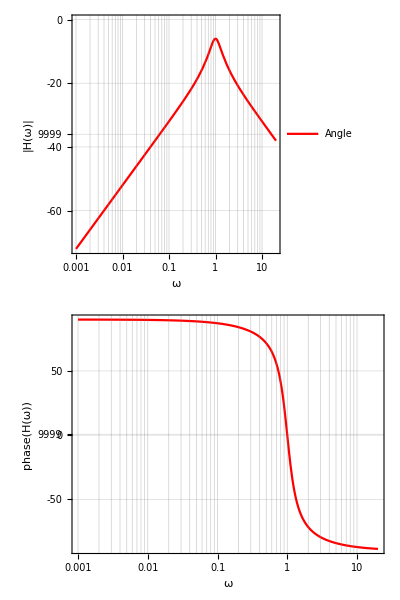

```mathematica
BodePlot[tf4,GridLines->Automatic,PlotStyle->Red,ImageSize->Large,FrameLabel->{{"ω","|H(ω)|"},{"ω","phase(H(ω))"}},PlotLegends->{"Angle"}]
```

#### Make a Bode-plot of the systems

With the function Manipulate you have the means to explore the effect of parameters in the system. Below you find an example of a second-order system where you can set the resonance frequency and the damping to explore the effect on the Bode diagram.

```mathematica
Manipulate[BodePlot[sys1/.{ζ->a,ω0->b},GridLines->Automatic,ImageSize->Medium],{{a,0.7},0,4},{{b,1},0,10}]
```

### Nyquist Plot

An alternative for the Bode-Plot is the so-called Nyquist plot. This represents the transfer function as a parametric plot in the complex plane, where ω is used as a parameter.

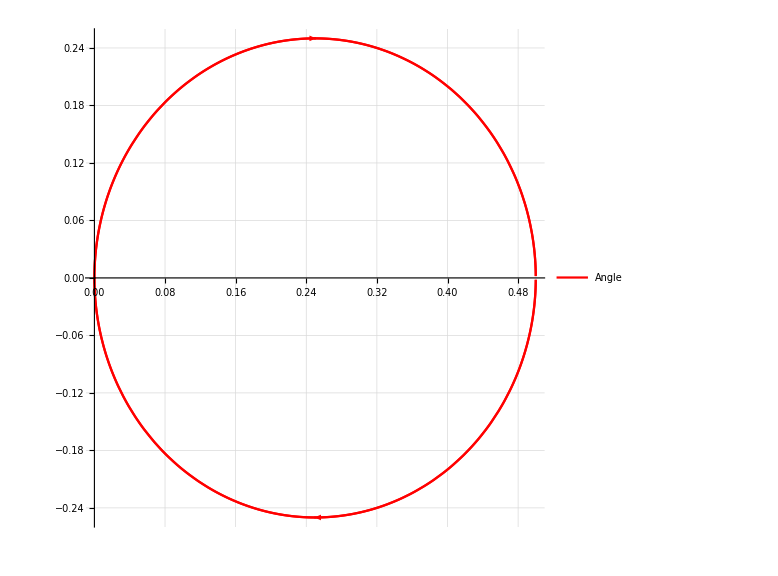

```mathematica
NyquistPlot[tf4,GridLines->Automatic,PlotStyle->Red,ImageSize->Large,FrameLabel->{{"ω","|H(ω)|"},{"ω","phase(H(ω))"}},PlotLegends->{"Angle"}]
```

Output Response

Now we define a few responses to the three standard inputs: Unit-Step, Delta function and Sine function (here we suppress the output, since we are only interested in the graphical representation , however it might be illustrative to view at the mathematical expressions, this can even be calculated form the general form (no values used for the parameters)):

```mathematica
tf4step=OutputResponse[{tf4,{0,0}},UnitStep[t],t];
tf4pulse=OutputResponse[{tf4,{0,0}},DiracDelta[t],t];
tf4sin = OutputResponse[{tf4,{0,0}},Sin[2 π t],t];
```

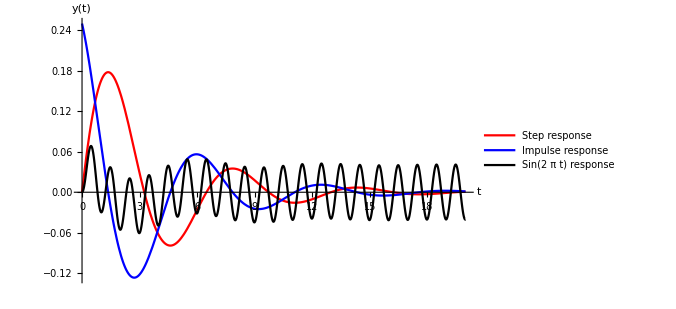

```mathematica
Plot[{tf4step,tf4pulse,tf4sin},{t,0,20},PlotRange->Full,PlotStyle->{Red,Blue,Black},AxesLabel->{"t","y(t)"},ImageSize->500,PlotLegends->{"Step response","Impulse response","Sin(2 π t) response"},BaseStyle->12]
```

Control Systems

## Stability

## Feed-back Systems

```mathematica
sys=TransferFunctionModel[s/((s+4)(s+5)),s]
```

s/((4+s) (5+s))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11$CellContext`s41FalseFalseFalseAutomaticNoneAutomatic

```mathematica
closedLoop=SystemsModelFeedbackConnect[sys]
```

s/(20+10 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11$CellContext`s201FalseFalseFalseAutomaticNoneAutomatic

```mathematica
First[Flatten[closedLoop[[1,1]]/closedLoop[[1,2]]]]
```

s/(20+10 s+s^2)

### Example of a Feedback loop

```mathematica
plant=TransferFunctionModel[s/(1.0+s),s]
```

s/(1.+s)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11$CellContext`s1.1FalseFalseFalseAutomaticNoneAutomatic

```mathematica
plantd=ToDiscreteTimeModel[plant,1,z,Method->"ZeroOrderHold"]
```

(1.-1. z)/(0.367879-1. z)1.TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z111.0.367879441171442331FalseFalseFalseAutomaticNoneAutomatic

```mathematica
d=ToDiscreteTimeModel[TransferFunctionModel[(s+1)/(s+5.0),s],1,z,Method->"ZeroOrderHold"]
```

(0.801348-1. z)/(0.00673795-1. z)1.TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z110.80134758939981670.0067379469990854711FalseFalseFalseAutomaticNoneAutomatic

```mathematica
sys=SystemsModelSeriesConnect[d,plantd]
```

((0.801348-1. z) (1.-1. z))/((0.00673795-1. z) (0.367879-1. z))1.TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z110.80134758939981670.0067379469990854711FalseFalseFalseAutomaticNoneNoneAutomatic

```mathematica
loopBack=SystemsModelFeedbackConnect[sys]
```

(1.5825×10^17 (-1.+1. z) (-0.801348+1. z))/(3.92264×10^14-5.92834×10^16 z+1.5825×10^17 z^2+1.5825×10^17 (-1.+1. z) (-0.801348+1. z))1.TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z111.5825042436963018e173.92263583864596e141FalseFalseFalseAutomaticNoneNoneAutomatic

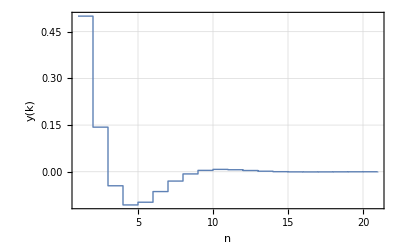

```mathematica
ListPlot[OutputResponse[loopBack,Table[1,{k,0,20}]],Joined->True,PlotRange->All,InterpolationOrder->0,Frame->True,PlotStyle->{Thick,Red},GridLines->Automatic,GridLinesStyle->Dashed,FrameLabel->{{"y(k)",None},{"n","plant response"}},RotateLabel->False]
```

```mathematica
ss=StateSpaceModel[loopBack]
```

01.0-0.4019131.087981.0.199717-0.3566830.51.StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneNoneAutomatic

```mathematica
poles=TransferFunctionPoles[loopBack]
```

{{{0.543991-0.325556 ⅈ,0.543991+0.325556 ⅈ}}}

```mathematica
Abs[#]&/@poles
```

{{{0.633966,0.633966}}}

## Root-locus

### Continuous-time system

```mathematica
sys=TransferFunctionModel[k*(s^2+2 s+4)/(s(s+4)(s+6)(s^2+1.4s+1)),s]
```

(4. k+2. k s+k s^2)/(24. s+43.6 s^2+39. s^3+11.4 s^4+s^5)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s114.24.1FalseFalseFalseAutomaticNoneAutomatic

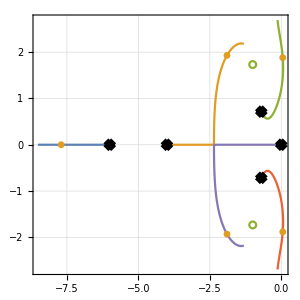

Syntax::sntxi: Incomplete expression; more input is needed .

```mathematica
RootLocusPlot[sys,{k,0,100},ImageSize->300,GridLines->Automatic,GridLinesStyle->Dashed,Frame->True,AspectRatio->1]
-
```

### Discrete-time system

```mathematica
sys=TransferFunctionModel[k(5s+1)/(s^2+2s+3),s]
```

(k (1+5 s))/(3+2 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11$CellContext`k31FalseFalseFalseAutomaticNoneAutomatic

```mathematica
samplePeriod=0.5;(*sec*)
```

```mathematica
sysd=ToDiscreteTimeModel[sys,samplePeriod,z]
```

(-19. k+2. k z+21. k z^2)/(11.-26. z+27. z^2)0.5TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z11-19.11.1FalseFalseFalseAutomaticNoneAutomatic

```mathematica
p1=RootLocusPlot[sysd,{k,0,100},ImageSize->300,GridLines->Automatic,GridLinesStyle->Dashed,Frame->True,AspectRatio->1,PlotPoints->200,PlotStyle->PointSize[0.01]];
```

```mathematica
p2=ParametricPlot[{Sin[t],Cos[t]},{t,0,2Pi},AspectRatio->1,GridLines->Automatic,GridLinesStyle->Dashed];
```

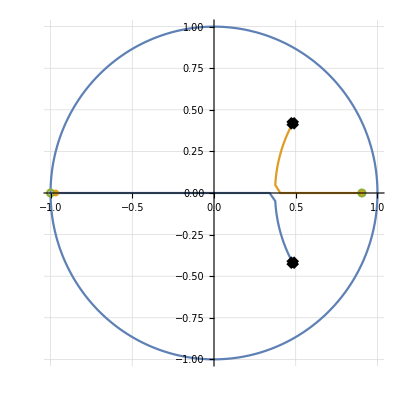

```mathematica
Show[p2,p1]
```

Fourier Transform (Continuous)

```mathematica
spec1[ω_]=FourierTransform[Cos[ω0 t],t,ω]
```

√(π/2) DiracDelta[ω-ω0]+√(π/2) DiracDelta[ω+ω0]

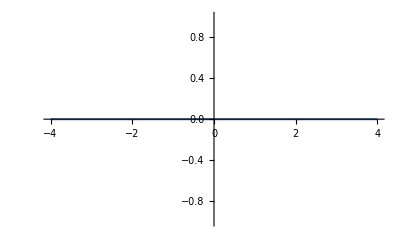

```mathematica
Plot[(spec1[ω]/.ω0->1),{ω,-4,4},Exclusions->None,ExclusionsStyle->{Red,Blue}]
```

The plot of the frequency spectrum can not be made, since the function DiracDelta is unevaluated at 0:

```mathematica
DiracDelta[0]
```

DiracDelta[0]

```mathematica
spec2[ω_]=FourierTransform[(HeavisideTheta[t+a]-HeavisideTheta[t-a]),t,ω]
```

(√(2/π) Sin[a ω])/ω

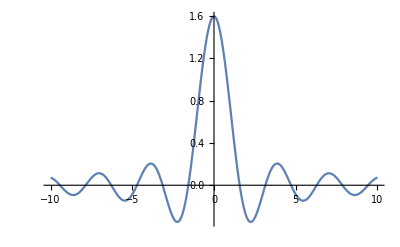

```mathematica
Plot[spec2[ω]/.a->2,{ω,-10,10},PlotRange->Full]
```

Fourier Series

Signals: Continuous and Discrete

## Discrete-time systems

Difference Equations

### Discrete State-Space Model

```mathematica
ss2=StateSpaceModel[{{{0,1,0,0},{-0.1,-0.001,0.1,0.001},{0,0,0,1}, {0.05,0.005,-0.5,-0.005}},{{0},{0},{0},{1}},{{1,0,0,0 }}}, SamplingPeriod->0.1]
```

01000-0.1-0.0010.10.0010000100.050.005-0.5-0.0051100000.1StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1141FalseFalseFalseAutomaticNoneAutomatic

Fourier Transform Discrete

```mathematica
(*Write down the h and take its DTFT*)
Clear[n,w]
h=1/4 DiscreteDelta[n+1]+1/2 DiscreteDelta[n]+1/4 DiscreteDelta[n-1];
hTransformed=FourierSequenceTransform[h,n,w]
```

1/4 ⅇ^(-ⅈ w) (1+ⅇ^(ⅈ w))^2

```mathematica
x=1 DiscreteDelta[n]+2 DiscreteDelta[n-1]-2 DiscreteDelta[n-2]+DiscreteDelta[n-3]+4 DiscreteDelta[n-4]-DiscreteDelta[n-5]+DiscreteDelta[n-6]+2 DiscreteDelta[n-7];
xTransformed=FourierSequenceTransform[x,n,w]
```

ⅇ^(-7 ⅈ w) (2+ⅇ^(ⅈ w)-ⅇ^(2 ⅈ w)+4 ⅇ^(3 ⅈ w)+ⅇ^(4 ⅈ w)-2 ⅇ^(5 ⅈ w)+2 ⅇ^(6 ⅈ w)+ⅇ^(7 ⅈ w))

```mathematica
z=InverseFourierSequenceTransform[xTransformed hTransformed,w,n]
```

Piecewise[{{-1/4, n==2}, {1/4, n==-1}, {1/2, n==8}, {3/4, n==1||n==5||n==6}, {1, n==0||n==3}, {5/4, n==7}, {2, n==4}, {0, True}}]

```mathematica
N@InverseFourierSequenceTransform[xTransformed hTransformed hTransformed,w,n]
```

Piecewise[{{0.0625, n==-2.}, {0.125, n==9.}, {0.3125, n==2.}, {0.375, n==-1.}, {0.5625, n==1.||n==8.}, {0.75, n==0.}, {0.875, n==6.}, {0.9375, n==3.||n==7.}, {1.0625, n==5.}, {1.4375, n==4.}, {0., True}}]

### DFT of sequence of numbers

```mathematica
Chop[Fourier[{1,2,3},FourierParameters->{1,-1}]]
```

{6.,-1.5+0.866025 ⅈ,-1.5-0.866025 ⅈ}

FIR-Filters

```mathematica
t=Table[{x,UnitBox[x/(0.9 π)]},{x,0,3,2π/11}]
```

{{0,1},{(2 π)/11,1},{(4 π)/11,1},{(6 π)/11,0},{(8 π)/11,0},{(10 π)/11,0}}

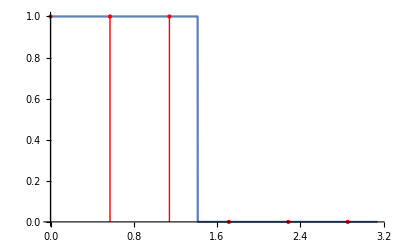

```mathematica
Show[{Plot[UnitBox[x/(0.9 π)],{x,0,π},Exclusions->None],ListPlot[t,PlotRange->All,PlotStyle->{Red,PointSize[Large]},Filling->0,FillingStyle->Red]}]
```

```mathematica
{frequencies,amplitudes}=Transpose[t];
FrequencySamplingFilterKernel[amplitudes,1]
```

{0.069411,-0.0540319,-0.10942,0.0473735,0.319394,0.454545,0.319394,0.0473735,-0.10942,-0.0540319,0.069411}

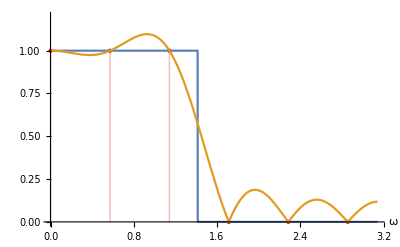

```mathematica
Show[{ListPlot[t,PlotRange->{{0,π},{0,1.2}},PlotStyle->{Red,PointSize[Medium]},Filling->Axis,AxesLabel->{ω,None}],Plot[{UnitBox[ω/(0.9 π)],Evaluate[Abs[ListFourierSequenceTransform[FrequencySamplingFilterKernel[amplitudes,1],ω]]]},{ω,0,π},PlotRange->{{0,π},All}]}]
```

Continuous-time ↔ Discrete-time

```mathematica
tfc=TransferFunctionModel[(s+1)/(s^2+1 s+1),s]
```

(1+s)/(1+s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11111FalseFalseFalseAutomaticNoneAutomatic

```mathematica
tfd=ToDiscreteTimeModel[tfc,0.1,z,Method->"ZeroOrderHold"]
```

(-0.0903292+0.0998375 z)/(0.904837-1.89533 z+z^2)0.1TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z11-0.090329166686017430.90483741803595961FalseFalseFalseAutomaticNoneAutomatic

```mathematica
{gm,pm}=GainPhaseMargins[tfd]
```

{{{31.4159,19.9833}},{{1.41451,1.83932},{0.,3.14159}}}

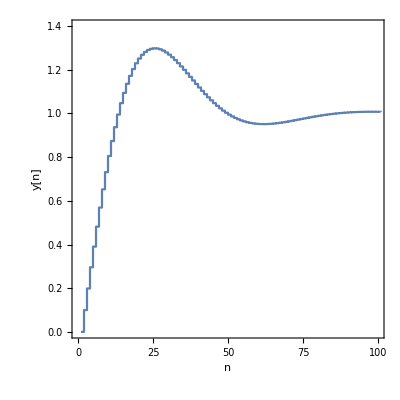

```mathematica
max=100;
yn=OutputResponse[tfd,Table[UnitStep[n],{n,0,max}]];
ListPlot[yn,Joined->True,InterpolationOrder->0,PlotRange->{{0,max},{0,1.4}},Frame->True,FrameLabel->{{"y[n]",None},{"n","unit step response"}},ImageSize->400,AspectRatio->1,BaseStyle->14]
```

z-Transform

```mathematica
ZTransform[UnitStep[n],n,z]
```

z/(-1+z)

### Inverse z-Transform

```mathematica
x[n_]:=InverseZTransform[z/(z-1),z,n]
```

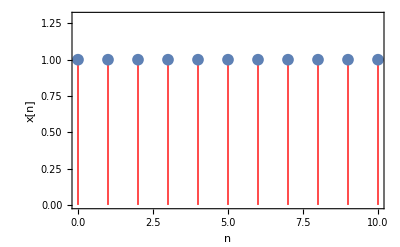

```mathematica
ListPlot[Table[{n,x[n]},{n,0,10}],Frame->True,FrameLabel->{{"x[n]",None},{"n","Inverse Ztransform of z/(z-1)"}},FormatType->StandardForm,RotateLabel->False,Filling->Axis,FillingStyle->Red,PlotRange->{Automatic,{0,1.3}},PlotMarkers->{Automatic,12}]
```

### Expanded example

```mathematica
nSamples=14;
f=1.0;
sampleTime=1/f;
u[t_]:=Sin[2*Pi*(f/3)*t]*Exp[-0.3*t]
ud[n_]:=u[n*sampleTime];
plant=TransferFunctionModel[(3 s)/((s+1)(s+2)),s];
sysd=ToDiscreteTimeModel[plant,sampleTime,z,Method->"ZeroOrderHold"]
```

(-0.697632+0.697632 z)/(0.0497871-0.503215 z+z^2)1.TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z11-0.69763247380448910.0497870683678641FalseFalseFalseAutomaticNoneAutomatic

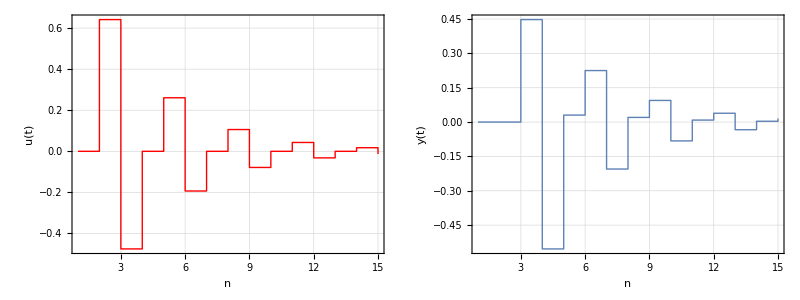

```mathematica
opts={Joined->True,PlotRange->All,AspectRatio->1,InterpolationOrder->0,ImageSize->200,Frame->True,PlotRange->{{0,nSamples},{-0.5,0.5}},GridLines->Automatic,GridLinesStyle->Dashed};
inputPlot=ListPlot[Table[ud[k],{k,0,nSamples}],Evaluate[opts],FrameLabel->{{"u(t)",None},{"n","plant input u(nT)"}},PlotStyle->{Thick,Red}];
plantPlot=ListPlot[OutputResponse[sysd,Table[ud[k],{k,0,nSamples}]],Evaluate[opts],FrameLabel->{{"y(t)",None},{"n","plant output y(nT)"}},PlotStyle->{Thick,Blue}];
Grid[{{inputPlot,plantPlot}}]
```

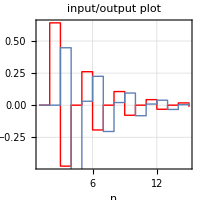

```mathematica
Show[{inputPlot,plantPlot},PlotLabel->"input/output plot"]
```

IIR-Filters

## Stochastic description of Signals

Statistics

## Convolution

### Example

```mathematica
x1={1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
x2={4,5,6}
```

{4,5,6}

```mathematica
ListConvolve[x2,x1,{1,-1},0]
```

{4,13,28,43,58,49,30}

## Correlation

### Example

```mathematica
a={0,0,2,-1,3,7,1,2,-3,0,0}
```

{0,0,2,-1,3,7,1,2,-3,0,0}

```mathematica
b={0,0,1,-1,2,-2,4,1,-2,5,0,0}
```

{0,0,1,-1,2,-2,4,1,-2,5,0,0}

```mathematica
c=Reverse[ListCorrelate[a,b,{-1,1},0]]
```

{0,0,0,0,10,-9,19,36,-14,33,0,7,13,-18,16,-7,5,-3,0,0,0,0}

## Items from the Models Section

## Feedback and Control

### Controllable State-Space

```mathematica
A0={{0,1,0,0},{0,0,-1,0},{0,0,0,1},{0,0,5,0}};
```

```mathematica
B0={{0},{1},{0},{-2}};
```

```mathematica
sys=StateSpaceModel[{A0,B0}];
```

```mathematica
m=ControllabilityMatrix[sys]
```

```mathematica
ControllableModelQ[sys]
```

```mathematica
MatrixRank[m]
```

## State-Space for non-linear Systems

### Define a non-linear State-Space model

```mathematica
nsys=NonlinearStateSpaceModel[{{u-Subscript[x, 1] Subscript[x, 2],u Subscript[x, 2]+1},{Subscript[x, 1]}},{Subscript[x, 1],Subscript[x, 2]},u]
```

u-x_1 x_21+u x_2x_1x_1x_2 2111NoneNoneFalseFalseFalse{u}Automatic

```mathematica
nsysn=OutputResponse[nsys,UnitStep[t],{t,0,5}];
```

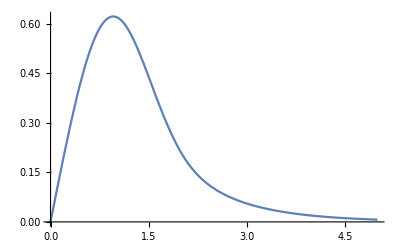

```mathematica
Plot[nsysn,{t,0,5}]
```

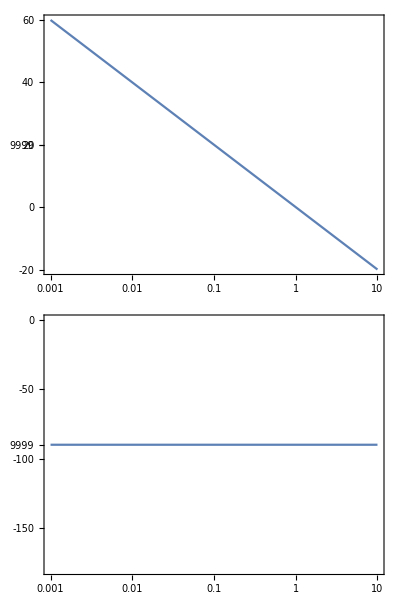

```mathematica
BodePlot[nsys]
```

```mathematica
nsysStep=OutputResponse[nsys,UnitStep[t],t];
```

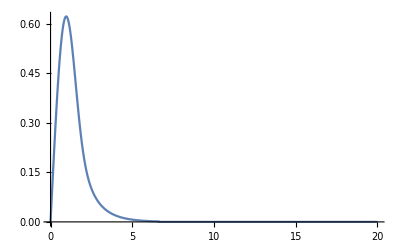

```mathematica
Plot[nsysStep,{t,0,20},PlotRange->All]
```

### The Van Der Pol equation

```mathematica
vdpeqn=y''[x]-μ (1-x^2) y'[x] + x== Sin[ ω t]
```

x-(1-x^2) μ y'[x]+y''[x]==Sin[t ω]

```mathematica
ssp=NonlinearStateSpaceModel[{vdpeqn}, y[x],x]
```

x-(1-x^2) μ y'[x]+y''[x]==Sin[t ω]y[x] 1110NoneFalseFalseFalse{x}Automatic

#### now the right way

```mathematica
vdpn=NonlinearStateSpaceModel[{{Subscript[y, 2],u-Subscript[y, 1]+μ (1-Subscript[y, 1]^2) Subscript[y, 2]},{Subscript[y, 1],Subscript[y, 2]}},{Subscript[y, 1],Subscript[y, 2]},u]
```

y_2u-y_1+μ (1-y_1^2) y_2y_1y_2y_1y_2 2122NoneNoneFalseFalseFalse{u}Automatic

```mathematica
vdpns=OutputResponse[(vdpn/.μ->0.8),{Sin[0.1+0.01 t]},{t,0,100}];
```

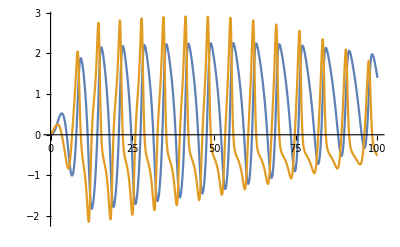

```mathematica
Plot[vdpns,{t,0,100}]
```

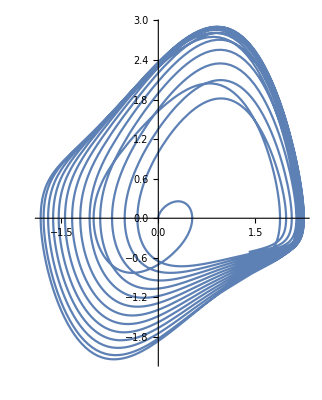

```mathematica
ParametricPlot[{vdpns[[1]],vdpns[[2]]},{t,0,100}]
```

```mathematica
ss4=TransferFunctionModel[vdpn,s]
```

1/(1-μ s+s^2)s/(1-μ s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s121$CellContext`s11FalseFalseFalseAutomaticNoneAutomatic

#### Lotka-Volterra model

```mathematica
npar={α->0.8,β->1.2,γ->0.4,δ->0.5}
```

{α→0.8,β→1.2,γ→0.4,δ→0.5}

```mathematica
inic={0.9,0.4}
```

{0.9,0.4}

```mathematica
inic={0.9,0.1}
```

{0.9,0.1}

```mathematica
nsys=NonlinearStateSpaceModel[{{α Subscript[x, 1] -β Subscript[x, 1] Subscript[x, 2]+u,-γ Subscript[x, 2]+ δ Subscript[x, 1] Subscript[x, 2]},{Subscript[x, 1],Subscript[x, 2]}},{Subscript[x, 1],Subscript[x, 2]},u]
```

u+α x_1-β x_1 x_2-γ x_2+δ x_1 x_2x_1x_2x_1x_2 2122NoneNoneFalseFalseFalse{u}Automatic

```mathematica
nsys/.npar
```

u+0.8 x_1-1.2 x_1 x_2-0.4 x_2+0.5 x_1 x_2x_1x_2x_1x_2 2122NoneNoneFalseFalseFalse{u}Automatic

```mathematica
nsysres=OutputResponse[{nsys/.npar,inic},0,{t,0,20}]
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

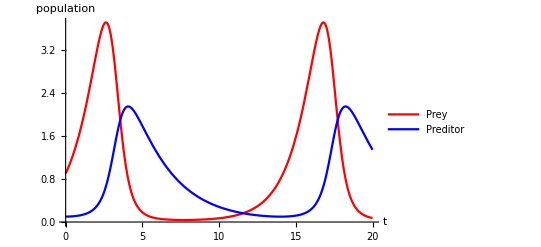

```mathematica
Plot[nsysres,{t,0,20},PlotStyle->{Red,Blue},AxesLabel->{"t","population"},PlotLegends->{"Prey","Preditor"}]
```

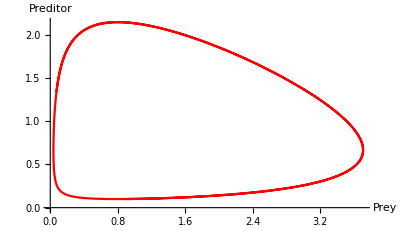

```mathematica
ParametricPlot[nsysres,{t,0,20},PlotStyle->Red,AxesLabel->{"Prey","Preditor"}]
```

## Additional State-Space examples

### Problem 3.4

Extended version: extra output.

```mathematica
ssm34=NonlinearStateSpaceModel[{Subscript[q, 1]'[t] == -4 Subscript[q, 1][t] + 10 Subscript[q, 2][t] + 4 u[t],Subscript[q, 2]'[t]== 1/2 Subscript[q, 1][t] - 2 Abs[Subscript[q, 2][t]] Subscript[q, 2][t]},{{Subscript[q, 1]'[t],0},{Subscript[q, 1][t],Subscript[q, 10]},{Subscript[q, 2]'[t],0},{Subscript[q, 2][t],Subscript[q, 20]}},{{u[t],Subscript[u, 0]}}, {Subscript[q, 1][t],Subscript[q, 2][t]},t]
```

4 u[t]-4 x_1[t]+10 x_2[t]1/2 (x_1[t]-4 Abs[x_2[t]] x_2[t])x_1[t]x_2[t]{x_1[t],q_10}{x_2[t],q_20} 2122NoneNoneFalseFalseFalse{{u[t],u_0}}t

```mathematica
ssm34lin=StateSpaceModel[ssm34]
```

-41041/21/2 (-4 Abs[q_20]-4 q_20 Abs'[q_20])0100010StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1221FalseFalseFalseAutomaticNone,{{x_1[t],0},{x_2[t],0}},{{u[t],0}},Automatic,t

```mathematica
tf34lin=TransferFunctionModel[ssm34lin]
```

(4 (s+2 Abs[q_20]+2 q_20 Abs'[q_20]))/(-5+4 s+s^2+8 Abs[q_20]+2 s Abs[q_20]+8 q_20 Abs'[q_20]+2 s q_20 Abs'[q_20])2/(-5+4 s+s^2+8 Abs[q_20]+2 s Abs[q_20]+8 q_20 Abs'[q_20]+2 s q_20 Abs'[q_20])TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s1242-51FalseFalseFalseAutomaticNoneAutomatic

#### exact problem

```mathematica
ssm34e=NonlinearStateSpaceModel[{Subscript[q, 1]'[t] == -4 Subscript[q, 1][t] + 10 Subscript[q, 2][t] + 4 u[t],Subscript[q, 2]'[t]== 1/2 Subscript[q, 1][t] - 2 Abs[Subscript[q, 2][t]] Subscript[q, 2][t]},{{Subscript[q, 1]'[t],0},{Subscript[q, 1][t],Subscript[q, 10]},{Subscript[q, 2]'[t],0},{Subscript[q, 2][t],Subscript[q, 20]}},{{u[t],Subscript[u, 0]}}, {Subscript[q, 2][t]},t]
```

4 u[t]-4 x_1[t]+10 x_2[t]1/2 (x_1[t]-4 Abs[x_2[t]] x_2[t])x_2[t]{x_1[t],q_10}{x_2[t],q_20} 2111NoneNoneFalseFalseFalse{{u[t],u_0}}t

```mathematica
ssm34elin=StateSpaceModel[ssm34e]
```

-41041/21/2 (-4 Abs[q_20]-4 q_20 Abs'[q_20])0010StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNone,{{x_1[t],0},{x_2[t],0}},{{u[t],0}},Automatic,t

```mathematica
tf34elin=TransferFunctionModel[ssm34elin]
```

2/(-5+4 s+s^2+8 Abs[q_20]+2 s Abs[q_20]+8 q_20 Abs'[q_20]+2 s q_20 Abs'[q_20])TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s112-51FalseFalseFalseAutomaticNone,{u[s]}

### Problem 3.6

```mathematica
aa=({{-3, -19}, {1, -2}})
```

{{-3,-19},{1,-2}}

```mathematica
bb=({{0}, {-1}})
```

{{0},{-1}}

```mathematica
cc=({{0, 2}})
```

{{0,2}}

```mathematica
dd={{0}}
```

{{0}}

```mathematica
ssm36=StateSpaceModel[{aa,bb,cc,dd}]
```

```mathematica
-3-1901-2-1020StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic
```

```mathematica
tf36=TransferFunctionModel[ssm36]
```

```mathematica
(-6-2 s)/(25+5 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s11-6251FalseFalseFalseAutomaticNoneAutomatic
```

```mathematica
ssm36ur=StateResponse[ssm36,UnitStep[t],t];
```

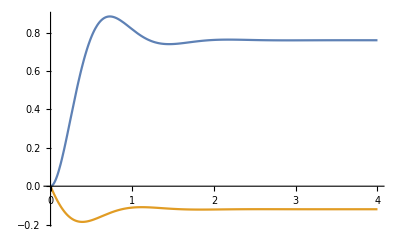

```mathematica
Plot[Evaluate[ssm36ur], {t, 0, 4}]
```

### Problem 3.7

```mathematica
ssm37=StateSpaceModel[{y''[t]+4 y'[t]+4 y[t] ==2 x'[t] + 2 x[t], 2 x'[t]+x[t]-y[t] ==u[t]},{{y''[t],0},{y'[t],0},{y[t],0},{x'[t],0},{x[t],0}},{{u[t],1}},{y[t],x[t]},t]
```

0100-3-4111/20-1/21/210000010StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1231FalseFalseFalseAutomaticNone,{{y[t],0},x_1,{x[t],0}},{{u[t],0}},Automatic,t

```mathematica
tf37=TransferFunctionModel[ssm37]
```

(2 (1+s))/(2+10 s+9 s^2+2 s^3)(4+4 s+s^2)/(2+10 s+9 s^2+2 s^3)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s122421FalseFalseFalseAutomaticNoneAutomatic

```mathematica
tf37poles=TransferFunctionPoles[tf37]
```

{{{1/2 (-3+(-9+2 ⅈ √237)^(1/3)/3^(2/3)+7/(3 (-9+2 ⅈ √237))^(1/3)),-3/2-((1+ⅈ √3) (-9+2 ⅈ √237)^(1/3))/(4 3^(2/3))-(7 (1-ⅈ √3))/(4 (3 (-9+2 ⅈ √237))^(1/3)),-3/2-((1-ⅈ √3) (-9+2 ⅈ √237)^(1/3))/(4 3^(2/3))-(7 (1+ⅈ √3))/(4 (3 (-9+2 ⅈ √237))^(1/3))}},{{1/2 (-3+(-9+2 ⅈ √237)^(1/3)/3^(2/3)+7/(3 (-9+2 ⅈ √237))^(1/3)),-3/2-((1+ⅈ √3) (-9+2 ⅈ √237)^(1/3))/(4 3^(2/3))-(7 (1-ⅈ √3))/(4 (3 (-9+2 ⅈ √237))^(1/3)),-3/2-((1-ⅈ √3) (-9+2 ⅈ √237)^(1/3))/(4 3^(2/3))-(7 (1+ⅈ √3))/(4 (3 (-9+2 ⅈ √237))^(1/3))}}}

```mathematica
N[tf37poles]
```

{{{-0.255356+1.11022×10^-16 ⅈ,-1.35542-1.11022×10^-16 ⅈ,-2.88923-5.55112×10^-17 ⅈ}},{{-0.255356+1.11022×10^-16 ⅈ,-1.35542-1.11022×10^-16 ⅈ,-2.88923-5.55112×10^-17 ⅈ}}}

```mathematica
tf37zeros=TransferFunctionZeros[tf37]
```

{{{-1}},{{-2,-2}}}

```mathematica
ssm37ur=StateResponse[ssm37,UnitStep[t],t];
```

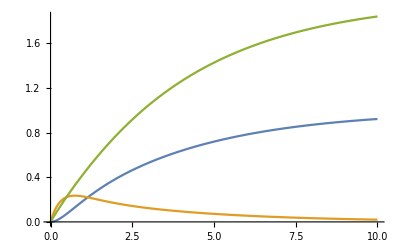

```mathematica
Plot[Evaluate[ssm37ur], {t, 0, 10}]
```

## Laplace versus direct solve

### Problem 9

#### Direct

```mathematica
InverseLaplaceTransform[(s^2+5 s + 1)/(s (s+1)^2(s+2)),s,t]
```

1/2 ⅇ^(-2 t) (5-6 ⅇ^t+ⅇ^(2 t)+6 ⅇ^t t)

```mathematica
Expand[%]
```

1/2+(5 ⅇ^(-2 t))/2-3 ⅇ^-t+3 ⅇ^-t t

#### Solve the differential equation in a direct way, including the initial conditions

```mathematica
dsol=DSolve[{y'''[t]+4 y''[t]+5 y'[t]+2 y[t] ==  UnitStep[t],y''[0]==1,y'[0]==1,y[0]== 0},y[t],t]
```

{{y[t]→ⅇ^(-2 t) (3-3 ⅇ^t+4 ⅇ^t t)+(-ⅇ^(-2 t) (3-3 ⅇ^t+4 ⅇ^t t)+1/2 ⅇ^(-2 t) (5-6 ⅇ^t+ⅇ^(2 t)+6 ⅇ^t t)) UnitStep[t]}}

```mathematica
y9ds[t_]=y[t]/.dsol//Expand
```

{3 ⅇ^(-2 t)-3 ⅇ^-t+4 ⅇ^-t t+UnitStep[t]/2-1/2 ⅇ^(-2 t) UnitStep[t]-ⅇ^-t t UnitStep[t]}

#### Solve the differential equation from the Laplace transform

```mathematica
ltdeqn=LaplaceTransform[y'''[t]+4 y''[t]+5 y'[t]+2 y[t] ==  UnitStep[t],t,s]
```

2 LaplaceTransform[y[t],t,s]+s^3 LaplaceTransform[y[t],t,s]+5 (s LaplaceTransform[y[t],t,s]-y[0])-s^2 y[0]+4 (s^2 LaplaceTransform[y[t],t,s]-s y[0]-y'[0])-s y'[0]-y''[0]==1/s

Apply the initial conditions

```mathematica
ltdeqn/.{y''[0]-> 1,y'[0]->1,y[0]->0}
```

-1-s+2 LaplaceTransform[y[t],t,s]+5 s LaplaceTransform[y[t],t,s]+s^3 LaplaceTransform[y[t],t,s]+4 (-1+s^2 LaplaceTransform[y[t],t,s])==1/s

Find an expression for the Laplace transform of the differential equation including the initial conditions.

```mathematica
Reduce[ltdeqn/.{y''[0]-> 1,y'[0]->1,y[0]->0},LaplaceTransform[y[t],t,s]]
```

s (1+s) (2+s)≠0&&LaplaceTransform[y[t],t,s]==(1+5 s+s^2)/(s (1+s)^2 (2+s))

Take the inverse Laplace transform of the result

```mathematica
y9l[t]=InverseLaplaceTransform[(1+5 s+s^2)/(s (1+s)^2 (2+s)),s,t]
```

1/2 ⅇ^(-2 t) (5-6 ⅇ^t+ⅇ^(2 t)+6 ⅇ^t t)

#### Plot both solutions in a single graph

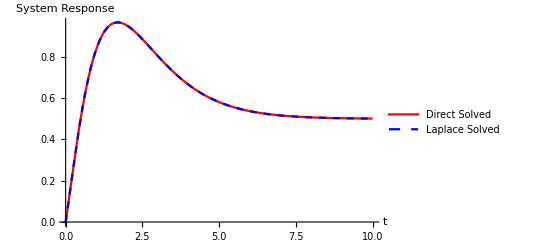

```mathematica
Plot[{y9ds[t],y9l[t]},{t,0,10},PlotStyle->{Red,{Blue,Dashed}},PlotLegends->{"Direct Solved","Laplace Solved"},AxesLabel->{"t","System Response"}]
```

Check for initial conditions:

```mathematica
initCalc={(D[y9l[t], t,t])/.t->0,(D[y9l[t], t])/.t->0,y9l[t]/.t->0}
```

{1,1,0}

Both methods give the same solutions, as it should be. The initial conditions also match.

## Calculate the Fourier Transform of two series

That differ only in the number of samples.

```mathematica
Subscript[ν, 1]=3; Subscript[ν, 2]=5; n=12; fs=300;
```

```mathematica
nn=3/2 2^n
```

6144

```mathematica
nm=2^n
```

4096

```mathematica
x1=Table[Sin[i 2 π Subscript[ν, 1]/fs]+Sin[i 2 π Subscript[ν, 2]/fs] ,{i,0,nn}];
```

```mathematica
tx1=Table[{(i/fs).Sin[i 2 π Subscript[ν, 1]/fs]+Sin[i 2 π Subscript[ν, 2]/fs] },{i,0,nn}];
```

```mathematica
x2=Table[Sin[i 2 π Subscript[ν, 1]/fs]+Sin[i 2 π Subscript[ν, 2]/fs] ,{i,0,nm}];
```

```mathematica
tx2=Table[{i/fs,Sin[i 2 π Subscript[ν, 1]/fs]+Sin[i 2 π Subscript[ν, 2]/fs]} ,{i,0,nm}];
```

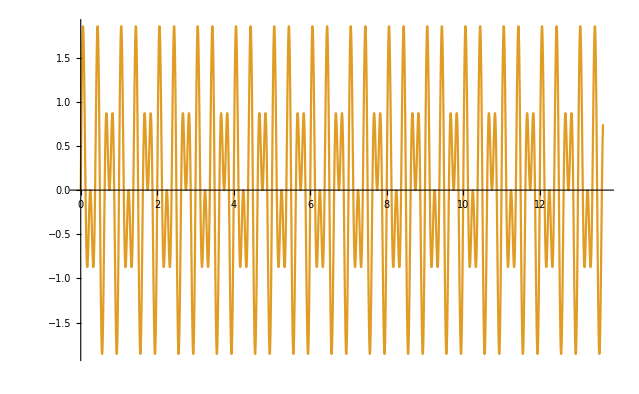

```mathematica
ListLinePlot[{tx1,tx2}]
```

```mathematica
ts1=nn/fs
```

512/25

```mathematica
ts2=nm/fs
```

1024/75

```mathematica
fx1=2 Abs[Fourier[x1]];
```

```mathematica
fx2=2 Abs[Fourier[x2]];
```

```mathematica
wxfx1=Table[{i/ts1,fx1[[i]]},{i,0, nn/2+1}];
```

```mathematica
wxfx2=Table[{i/ts2,fx2[[i]]},{i,0, nm/2+1}];
```

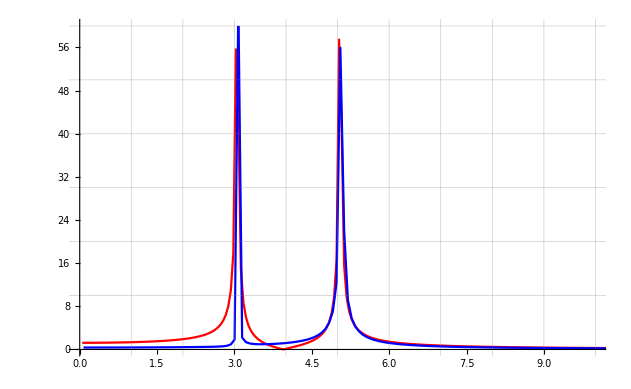

```mathematica
ListLinePlot[{wxfx1,wxfx2},PlotRange->{{0,10},{0,60}},PlotStyle->{Red,Blue},GridLines->{{1,2,3,4,5,6,7,8,9,10}, {10,20,30,40,50,60}}]
```

```mathematica
time=3/2 2^n
```

6144

```mathematica
1/time 30
```

5/1024

## Outlook

In module 4 there is not much computer work, i.e. you have to do all the work analytically, however, in module 5, traditionally we used Matlab and Simulink, however I regard Mathematica as a better alternative. Although not officially decided on, I will strongly plea for the use of Mathematica with Module 5, including in tests, where we traditionally allowed the use of Matlab and Simulink.